```mathematica
Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;
```

```mathematica
(* The total angular momentum quantum number is conserved, so we solve only for a specific J0 *)
J0=0;
(* The full two-body energy cutoff for the basis *)
EMax=22;(*=NMax+3*)
(* Easiest to set a value of a at the beginning so that the matrix elements become numerical *)
a=1;
(* This is needed because the eigensolver finds the eigenvalues with the smallest magnitude. Choose a postive number at least the size of the most negative eigenvalue expected *)
EOffset=50;
```

```mathematica
(* Determine the two body l=0 center of mass eigenenergies in the absence of SOC from Busch formula *)
If[a!=0,
νValues=Table[FindRoot[Sqrt[2]Gamma[-ν]/Gamma[-ν-1/2]==1/a,{ν,νGuess},AccuracyGoal->30],{νGuess,-2,(EMax/2-.75)+.25,.05*Sqrt[2]}];
νValues=DeleteDuplicates[νValues,Abs[ReplaceAll[ν,#1]-ReplaceAll[ν,#2]]<=.1&];,
νValues=Table[{ν->i},{i,0,EMax-3}] (* Handle a=0 case *);]

EValues=Sort[2.ν+3/2/.νValues] ;(* List of l=0 energies under the cutoff *)
νValues=Sort[Flatten[ν/.νValues]];
```

```mathematica
(* List of Busch quantum numbers under the energy cutoff *)
νValues
```

{-1.19964,0.310307,1.35611,2.37913,3.39367,4.40394,5.4117,6.41783,7.42283,8.42702,9.43059,10.4337}

```mathematica
(* List of Busch 2-body CoM Energies below the cutoff *)
EValues
```

{-0.899286,2.12061,4.21222,6.25825,8.28734,10.3079,12.3234,14.3357,16.3457,18.354,20.3612,22.3674}

```mathematica
(* Indexing of states *)
Clear[ni,li,Ni,Li,si,ji,Ji];
imax=0;
i=0;
verbose=False;

If[EValues[[1]]≤3/2,δEMax=EValues[[1]]-3/2,δEMax=0]; 
For[EShell=3,EShell≤EMax,++EShell,
For[N0=0,2N0+3+δEMax≤EShell,++N0,
For[L=0,2 N0+L+3+δEMax≤EShell,++L,
For[s=0,s≤1,++s,
For[j=Max[J0-L,0],j-L≤J0,++j,
For[l=0,l<=Max[EShell-2N0-L-3/2-EValues[[1]],EShell-2N0-L-3],++l,
If[l==0&&s==0,
For[ii=1,2N0+L+3/2+EValues[[ii]]≤EShell&&ii≤Length[EValues],++ii,
If[(EShell-1<2N0+L+3/2+EValues[[ii]]||EShell==3)&&2N0+L+3/2+EValues[[ii]]≤EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;
Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=νValues[[ii]];
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2*ni[i]+3/2];](* End If[Verbose] *)
](* End If[EvenQ... ] *)
] (* End ii loop *)(* End l==0 case, ν loop*),
For[n=0,2n+l+3/2+2N0+L+3/2≤EShell,++n,
If[EvenQ[l+s]&&2(N0+n)+L+l+3==EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;

Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=n;
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2ni[i]+l+3/2];](* End If[Verbose] *)
] (* End If[EvenQ...] *)
](* End For[n=0...] *)
] (* End If[l==0] *)
](* End l loop *)
] (* End j loop *)
] (* End s loop *)
] (* End L loop *)
];(* End N0 loop *)
iShell[EShell]=imax;
] (* End EShell loop *)
Clear[i,ii,l,L,N0,n,s,j];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 451 included states.

{{4,4},{5,6},{6,11},{7,15},{8,24},{9,31},{10,45},{11,56},{12,76},{13,92},{14,119},{15,141},{16,176},{17,205},{18,249},{19,286},{20,340},{21,386},{22,451}}

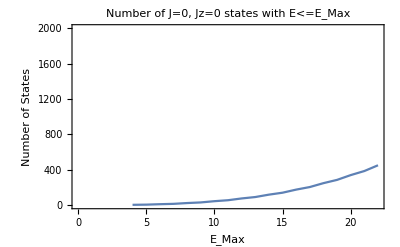

```mathematica
shellSizeTableWeyl=Table[{EShell,iShell[EShell]},{EShell,4,Min[32,EMax]}]
ListPlot[shellSizeTableWeyl,Joined->True,PlotRange->{{0,Min[32,EMax]},{0,2000}},Axes->False,Frame->True,PlotLabel->"Number of J=0, Jz=0 states with E<=E_Max",FrameLabel->{"E_Max","Number of States"}]
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=N[ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}]];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=N[SixJSymbol[{j1,j2,j3},{j4,j5,j6}]];
```

```mathematica
(* Normalization factor for Busch wave functions *)
A[ν_]:=A[ν]=N[((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2)];
```

```mathematica
(* This is the actual reduced matrix element of Q *)
Q[n1_,l1_,n_,l_]:= If[Abs[l1-l]==1,(I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
(* This is the actual reduced matrix element of q, accounting for the Busch states at l=0 *)
q[n1_,l1_,n_,l_]:=
If[l1==0&&l==1&&a≠0,Conjugate[q[n,1,n1,0]], (* Recursive definition for < ν l1=0 ||q || n l=1 > case *)
If[l1==1&&l==0&&a≠0, (* Definition for < n1 l1=1 ||q || ν l=0 > case *)I A[n]Gamma[-n]Sqrt[(n1!Gamma[n1+5/2])/(2 π^3)]Sum[(-1)^m/((n1-m)!Gamma[2+m-n])(n-(m+1)/2),{m,0,n1}],
(* Case where neither l or l1=0 *)
Q[n1,l1,n,l]]];
```

```mathematica
(* Matrix elements of σ.q *)
σq[n1_,s1_,l1_,n_,s_,l_,j_]:=  Sqrt[6](-1)^(l+s1+j)JSix[{j,s1,l1},{1,l,s}](s1-s)q[n1,l1,n,l];
```

```mathematica
(* Matrix elements of Σ.Q *)
ΣQ[N1_,l1_,j1_,L1_,N_,l_,s_,j_,L_,J_]:= Sqrt[12(2j1+1)(2j+1)](-1)^(L1+1)Q[N1,L1,N,L]Sum[(-1)^J2(2J2+1)JSix[{l,1,j1},{L1,J,J2}]JSix[{l,1,j},{L,J,J2}]JSix[{J2,1,L1},{1,L,1}],{J2,Abs[L-s],Abs[L+s]}]
```

```mathematica
(* Matrix σ.q+Σ.Q, stored as SparseArray *)
Clear[α]
Print["There are a total of ",imax," ","included states."]
σqΣQ=Table[0,{i,1,imax},{j,1,imax}];
Timing[For[i=1,i≤imax,++i,
If[i/50∈Integers,Print[i]];
For[j=1,j<i,j++,
σqΣQ[[i,j]]=KroneckerDelta[Ji[i],Ji[j]](KroneckerDelta[Ni[i],Ni[j]]KroneckerDelta[Li[i],Li[j]]KroneckerDelta[ji[i],ji[j]]σq[ni[i],si[i],li[i],ni[j],si[j],li[j],ji[j]]+KroneckerDelta[ni[i],ni[j]]KroneckerDelta[li[i],li[j]]KroneckerDelta[si[i],1]KroneckerDelta[si[j],1]ΣQ[Ni[i],li[i],ji[i],Li[i],Ni[j],li[j],si[j],ji[j],Li[j],Ji[j]]);
]
]
]
σqΣQ=SparseArray[σqΣQ+ConjugateTranspose[σqΣQ]];
```

There are a total of 451 included states.

50

100

150

200

250

300

350

400

450

{140.17692,Null}

```mathematica
(* Matrix of Subscript[H, HO]+Subscript[H, contact], stored as SparseArray *)
H0=SparseArray[DiagonalMatrix[Table[2ni[i]+2Ni[i]+li[i]+Li[i]+3+EOffset,{i,1,imax}]]];
```

```mathematica
αMin=0;αMax=1.5;αStep=1/100;
nEigValues=20;
Timing[For[α0=αMin,α0≤αMax,α0+=αStep,Energies[N[α0]]=Sort[Eigenvalues[N[Chop[SparseArray[H0+α0 σqΣQ]]],-nEigValues]]]]
Data[j_]:=Table[{α,Energies[N[α]][[j]]-EOffset},{α,αMin,αMax,αStep}];
```

{15.65664,Null}

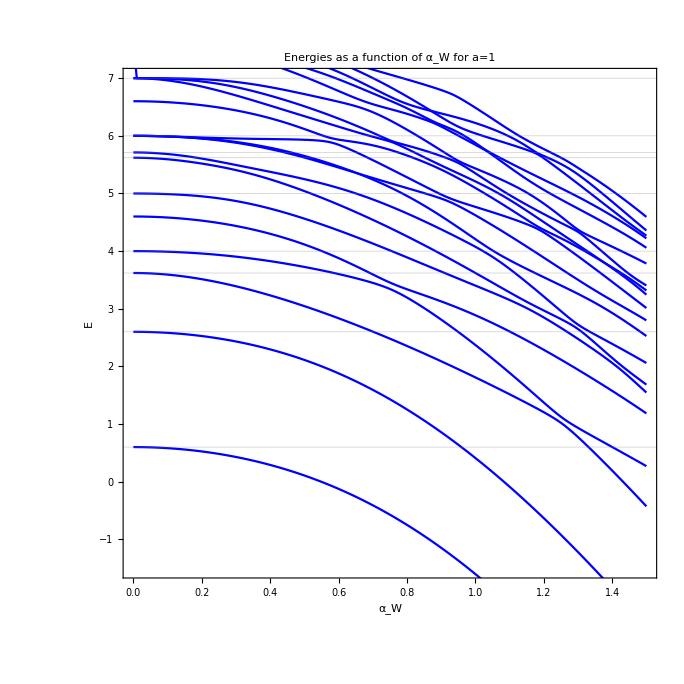

```mathematica
(* Plot of energies as a function of Subscript[α, Weyl] *)
ListPlot[Table[Data[i],{i,1,nEigValues,1}],Joined->True,PlotRange->{{αMin,αMax},{-1.5,7}},Frame->True,FrameLabel->{"α_W","E"},PlotStyle->Directive[Blue],GridLines->{{},Join[EValues+3/2,EValues+7/2,Table[i+3,{i,1,EMax-4}]]},AspectRatio->1.0,PlotLabel->StringJoin["Energies as a function of α_W for a=",ToString[a]]]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=0.5;
Convergence1={};
Convergence2={};
Convergence3={};
Convergence4={};
Convergence5={};
Convergence6={};
Convergence7={};
Convergence8={};
For[Emax=6,Emax≤EMax,Emax+=2,
H=Normal[H0+αTest σqΣQ];
H=Chop[N[SparseArray[H[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
AppendTo[Convergence1,{Emax,Eigenvalues[H,-8][[-1]]-EOffset}];
AppendTo[Convergence2,{Emax,Eigenvalues[H,-8][[-2]]-EOffset}];
AppendTo[Convergence3,{Emax,Eigenvalues[H,-8][[-3]]-EOffset}];
AppendTo[Convergence4,{Emax,Eigenvalues[H,-8][[-4]]-EOffset}];
AppendTo[Convergence5,{Emax,Eigenvalues[H,-8][[-5]]-EOffset}];
AppendTo[Convergence6,{Emax,Eigenvalues[H,-8][[-6]]-EOffset}];
AppendTo[Convergence7,{Emax,Eigenvalues[H,-8][[-7]]-EOffset}];
AppendTo[Convergence8,{Emax,Eigenvalues[H,-8][[-8]]-EOffset}];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.135177

0.00893379

0.000818979

0.000436872

0.00520424

0.000350042

0.000444132

0.000322203

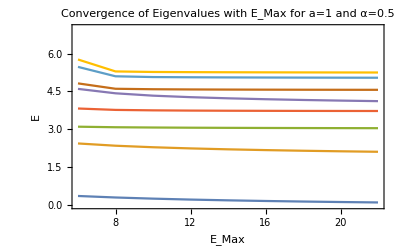

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{0,7}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=1;
Convergence1={};
Convergence2={};
Convergence3={};
Convergence4={};
Convergence5={};
Convergence6={};
Convergence7={};
Convergence8={};
For[Emax=6,Emax≤EMax,Emax+=2,
H=Normal[H0+αTest σqΣQ];
H=Chop[N[SparseArray[H[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
AppendTo[Convergence1,{Emax,Eigenvalues[H,-8][[-1]]-EOffset}];
AppendTo[Convergence2,{Emax,Eigenvalues[H,-8][[-2]]-EOffset}];
AppendTo[Convergence3,{Emax,Eigenvalues[H,-8][[-3]]-EOffset}];
AppendTo[Convergence4,{Emax,Eigenvalues[H,-8][[-4]]-EOffset}];
AppendTo[Convergence5,{Emax,Eigenvalues[H,-8][[-5]]-EOffset}];
AppendTo[Convergence6,{Emax,Eigenvalues[H,-8][[-6]]-EOffset}];
AppendTo[Convergence7,{Emax,Eigenvalues[H,-8][[-7]]-EOffset}];
AppendTo[Convergence8,{Emax,Eigenvalues[H,-8][[-8]]-EOffset}];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.0762175

0.224141

0.00672137

0.0432848

0.00889278

0.00602426

0.00104824

0.00232162

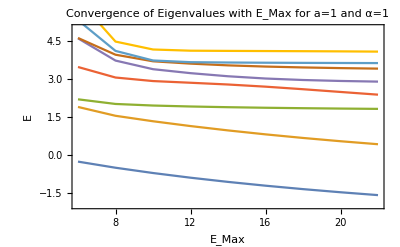

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-2,5}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```

```mathematica
(* Create lists of eigenvalues for different EMax *)
Clear[i];
αTest=2;
Convergence1={};
Convergence2={};
Convergence3={};
Convergence4={};
Convergence5={};
Convergence6={};
Convergence7={};
Convergence8={};
For[Emax=6,Emax≤EMax,Emax+=2,
H=Normal[H0+αTest σqΣQ];
H=Chop[N[SparseArray[H[[1;;iShell[Emax],1;;iShell[Emax]]]]]];
AppendTo[Convergence1,{Emax,Eigenvalues[H,-8][[-1]]-EOffset}];
AppendTo[Convergence2,{Emax,Eigenvalues[H,-8][[-2]]-EOffset}];
AppendTo[Convergence3,{Emax,Eigenvalues[H,-8][[-3]]-EOffset}];
AppendTo[Convergence4,{Emax,Eigenvalues[H,-8][[-4]]-EOffset}];
AppendTo[Convergence5,{Emax,Eigenvalues[H,-8][[-5]]-EOffset}];
AppendTo[Convergence6,{Emax,Eigenvalues[H,-8][[-6]]-EOffset}];
AppendTo[Convergence7,{Emax,Eigenvalues[H,-8][[-7]]-EOffset}];
AppendTo[Convergence8,{Emax,Eigenvalues[H,-8][[-8]]-EOffset}];]
```

```mathematica
(* Fractional convergence of eigenvalues at EMax compared to EMax-2 *)
conv[Convergence_]:=Abs[(Convergence[[-1,2]]-Convergence[[-2,2]])/Convergence[[-2,2]]];
conv[Convergence1]
conv[Convergence2]
conv[Convergence3]
conv[Convergence4]
conv[Convergence5]
conv[Convergence6]
conv[Convergence7]
conv[Convergence8]
```

0.088812

0.127807

0.204346

0.148173

0.240829

0.145296

0.0584309

1.69566

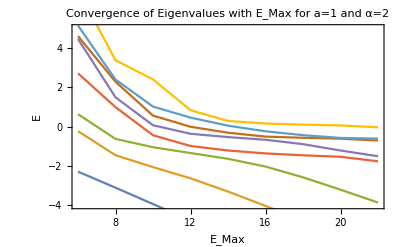

```mathematica
(* Make convergence plots *)
ListPlot[{Convergence1,Convergence2,Convergence3,Convergence4,Convergence5,Convergence6,Convergence7,Convergence8},Joined->True,Axes->False,Frame->True,PlotRange->{{6,EMax},{-4,5}},PlotLabel->StringJoin["Convergence of Eigenvalues with E_Max for a=", ToString[a]," and α=",ToString[αTest]],FrameLabel->{"E_Max","E"}]
```